# Quantum Computing Circuits

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx  
With contributions by Francisco Delgado-Cepeda and Sergio E. Martínez-Casas

## Introduction

This is a tutorial on the use of Quantum`Computing` Mathematica add-on to generate and work with Quantum Computing Circuits.

## Load the Package

First load the Quantum`Computing` package. Write:
Needs["Quantum`Computing`"];
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package. The semicolon prevents Mathematica from printing the welcome message:

```mathematica
Needs["Quantum`Computing`"]
```

Quantum`Computing` Version 2.2.0. (June 2010) 
A Mathematica package for Quantum Computing in Dirac bra-ket notation and plotting of quantum circuits
by José Luis Gómez-Muñoz

Execute SetComputingAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetComputingAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetComputingAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetComputingAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetComputingAliases[];
```

## Simple Quantum Computing Circuits

In order to plot a simple quantum circuit, press the keys:
QuantumPlot[ [ESC]cnot[ESC] [ESC]on[ESC] [ESC]hg[ESC] ]
Then press the [TAB] key several times to select the first "place holder" □, and press the keys:
1[TAB]2[TAB]1
then press at the same time the keys ⇧-⌤ to evaluate:

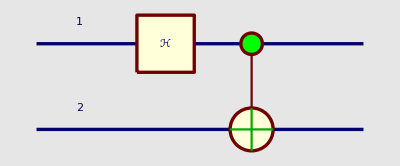

```mathematica
QuantumPlot[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]]
```

Quantum Circuits can be used exactly the same way as the Dirac expressions that were used to generate them.
As an example, write:
QuantumEvaluate[ ]
then copy-paste the circuit inside the brackets. Place the cursor to the right of the circuit and press the keys:
[ESC]on[ESC] [ESC]qqket[ESC]
Then press the [TAB] key one or several times to select the first "place holder" □, and press the keys:
0[TAB]1[TAB]0[TAB]2
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
QuantumEvaluate[ -Graphics-·|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩]
```

(|0_OverHat[1],0_OverHat[2]⟩)/(√2)+(|1_OverHat[1],1_OverHat[2]⟩)/(√2)

It is the same result that is obtained with the original Dirac expression, press the keys:
QuantumEvaluate[ [ESC]cnot[ESC] [ESC]on[ESC] [ESC]hg[ESC] [ESC]on[ESC][ESC]qqket[ESC] ]
Then press the [TAB] key several times to select the first "place holder" □, and press the keys:
1[TAB]2[TAB]1[TAB]0[TAB]1[TAB]0[TAB]2
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
QuantumEvaluate[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩]
```

(|0_OverHat[1],0_OverHat[2]⟩)/(√2)+(|1_OverHat[1],1_OverHat[2]⟩)/(√2)

In order to plot in 3D a simple quantum circuit, press the keys:
QuantumPlot3D[ [ESC]cnot[ESC] [ESC]on[ESC] [ESC]hg[ESC] ]
Then press the [TAB] key several times to select the first "place holder" □, and press the keys:
1[TAB]2[TAB]1
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
QuantumPlot3D[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]]
```

-Graphics3D-

Quantum Circuits can be used exactly the same way as the Dirac expressions that were used to generate them.
As an example, write:
QuantumMatrixForm[ ]
then copy-paste the circuit from the Mathematica output inside the brackets. Finally press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
QuantumMatrixForm[-Graphics3D-]
```

(1/(√2) | 0 | 1/(√2) | 0
0 | 1/(√2) | 0 | 1/(√2)
0 | 1/(√2) | 0 | -1/(√2)
1/(√2) | 0 | -1/(√2) | 0)

The same result is obtained from the original Dirac expression:

```mathematica
QuantumMatrixForm[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]]
```

(1/(√2) | 0 | 1/(√2) | 0
0 | 1/(√2) | 0 | 1/(√2)
0 | 1/(√2) | 0 | -1/(√2)
1/(√2) | 0 | -1/(√2) | 0)

Remember that QuantumMatrixForm is only for display purposes. For actual Mathematica calculations, QuantumMatrix must be used:

```mathematica
QuantumMatrix[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]]
```

{{1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)},{0,1/(√2),0,-1/(√2)},{1/(√2),0,-1/(√2),0}}

This is a Determinant, calculated from QuantumMatrix, not from QuantumMatrixForm

```mathematica
Det[QuantumMatrix[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]]]
```

-1

This is a normal power of a Quantum Circuit. Press [ESC]po[ESC] for the  normal power template and copy-paste the circuit from a previous Mathematica output. Write a 3 in the exponent:

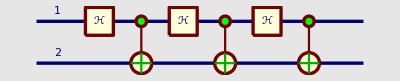

```mathematica
QuantumPlot[(-Graphics-)^3]
```

This is a tensor power of a Quantum Circuit. Press [ESC]tpow[ESC] for the tensor power template and copy-paste the circuit from the Mathematica output. Write a 3 in the exponent:

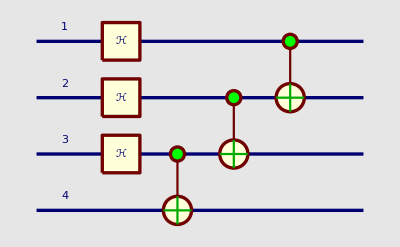

```mathematica
QuantumPlot[(-Graphics-)^(⊗3)]
```

The option QuantumGateShifting→False can be used to show the circuit in another, equivalent form (the arrow → can be entered by pressing [ESC]->[ESC])

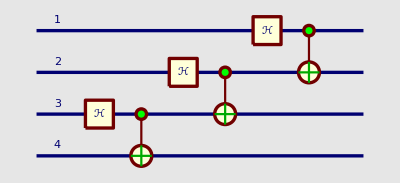

```mathematica
QuantumPlot[(-Graphics-)^(⊗3),QuantumGateShifting->False]
```

Here is another tensor power of the circuit, where the "exponent" is actually a list that defines the first qubit for each "factor":

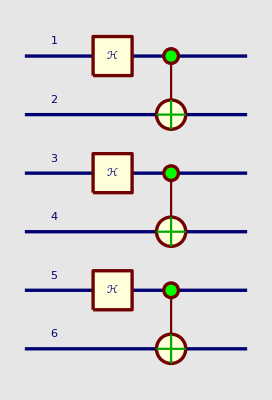

```mathematica
QuantumPlot[(-Graphics-)^(⊗{1,3,5})]
```

This is the same circuit obtained from the Dirac expression:

```mathematica
QuantumPlot[((𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]])^(⊗{1,3,5})]
```

-Graphics-

This circuit is similar to the previous one, but it looks different with the default qubit order:

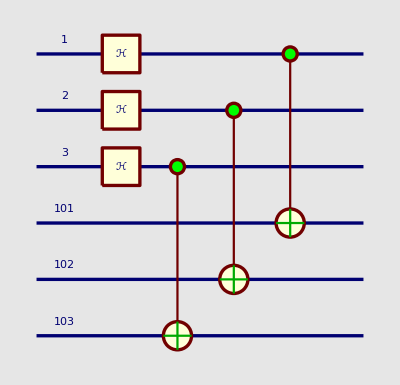

```mathematica
QuantumPlot[((𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[101]]]·Subscript[ℋ, OverHat[1]])^(⊗3)]
```

Using the option QubitList we can rearrange the circuit:

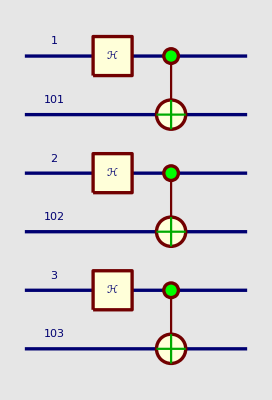

```mathematica
QuantumPlot[((𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[101]]]·Subscript[ℋ, OverHat[1]])^(⊗3),
QubitList->{1,101,2,102,3,103}]
```

The qubit labels can be hidden using the option QubitLabels:

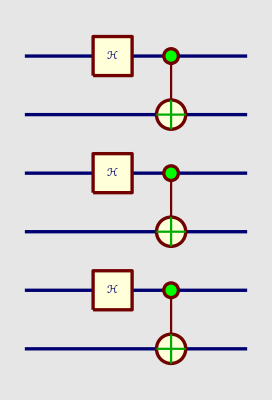

```mathematica
QuantumPlot[((𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[101]]]·Subscript[ℋ, OverHat[1]])^(⊗3),
QubitList->{1,101,2,102,3,103},
QubitLabels->False]
```

In order to plot a quantum circuit with initial (nonentangled) values for the qubits, press the keys:
QuantumPlot[ [ESC]cnot[ESC] [ESC]on[ESC] [ESC]hg[ESC] [ESC]on[ESC][ESC]qqket[ESC] ]
Then press the [TAB] key several times to select the first "place holder" □, and press the keys:
1[TAB]2[TAB]1[TAB]0[TAB]1[TAB]0[TAB]2
then press at the same time the keys ⇧-⌤ to evaluate:

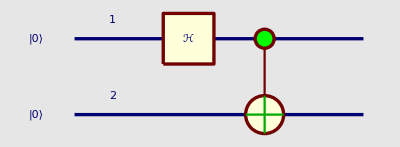

```mathematica
QuantumPlot[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩]
```

Qubit labels and initial qubit values do not need to be numbers:

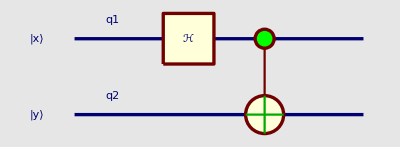

```mathematica
QuantumPlot[(𝒞^{OverHat[q1]})[Subscript[𝒩𝒪𝒯, OverHat[q2]]]·Subscript[ℋ, OverHat[q1]]·|Subscript[x, OverHat[q1]],Subscript[y, OverHat[q2]]⟩]
```

Use the option QubitLabels->False in order to have the plot without the qubit labels:

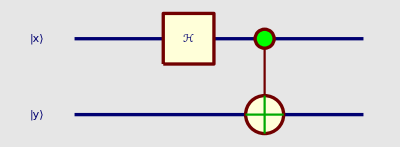

```mathematica
QuantumPlot[(𝒞^{OverHat[q1]})[Subscript[𝒩𝒪𝒯, OverHat[q2]]]·Subscript[ℋ, OverHat[q1]]·|Subscript[x, OverHat[q1]],Subscript[y, OverHat[q2]]⟩,QubitLabels->False]
```

You can also have the Dirac notation for the circuit:

```mathematica
QuantumEvaluate[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]]
```

(|0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|)/(√2)+(|1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|)/(√2)+(|0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|)/(√2)+(|1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|)/(√2)+(|0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|)/(√2)-(|1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|)/(√2)+(|0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|)/(√2)-(|1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|)/(√2)

TraditionalForm gives a format closer to the the format used in papers and textbooks:

```mathematica
TraditionalForm[QuantumEvaluate[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]]]
```

(|00⟩⟨00|)/(√2)+(|11⟩⟨00|)/(√2)+(|01⟩⟨01|)/(√2)+(|10⟩⟨01|)/(√2)+(|00⟩⟨10|)/(√2)-(|11⟩⟨10|)/(√2)+(|01⟩⟨11|)/(√2)-(|10⟩⟨11|)/(√2)

In order to plot the circuit of a tensor product of FREDKIN gates, press the keys:
QuantumPlot[ [ESC]tprod[ESC] ]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
 j[TAB]1[TAB]3[TAB]
Then press the keys:
[ESC]fred[ESC]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
j [TAB] j+1[TAB]j+2
then press at the same time the keys ⇧-⌤ to evaluate:

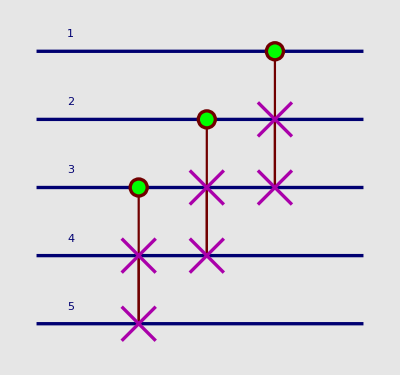

```mathematica
QuantumPlot[⊗_(j=1)^3 Subscript[ℱℛℰ𝒟𝒦ℐ𝒩, ĵ,OverHat[j+1],OverHat[j+2]]]
```

Use the option QubitList in order to have the plot with some (or all) wires in a differente order. Press the keys [ESC]qb[ESC] in order to enter the qubit template:

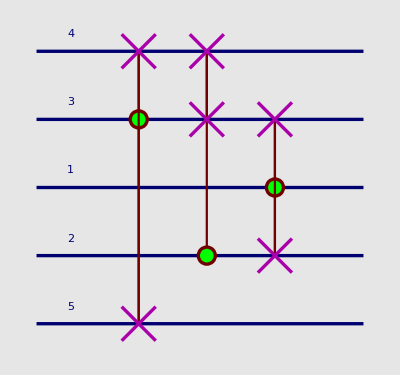

```mathematica
QuantumPlot[⊗_(j=1)^3 Subscript[ℱℛℰ𝒟𝒦ℐ𝒩, ĵ,OverHat[j+1],OverHat[j+2]],QubitList->{OverHat[4],OverHat[3]}]
```

## The Notation ℋ_{OverHat[q1],OverHat[q2]} for Plotting Quantum Gates in the Same Column

Notice that the three Hadamard gates are not in a column:

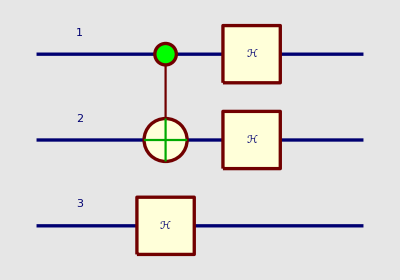

```mathematica
QuantumPlot[(Subscript[ℋ, OverHat[1]])^(⊗3)·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]]
```

Notice that the Hadamard gates are not in a column:

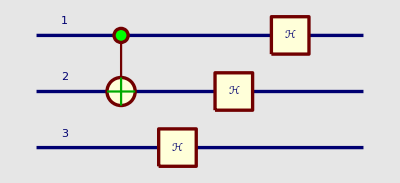

```mathematica
QuantumPlot[(Subscript[ℋ, OverHat[1]])^(⊗3)·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]],QuantumGateShifting->False]
```

There is a notation that allows to have all the ℋ gates in the same column. 
Press the keys [ESC]hggg[ESC] for the template:

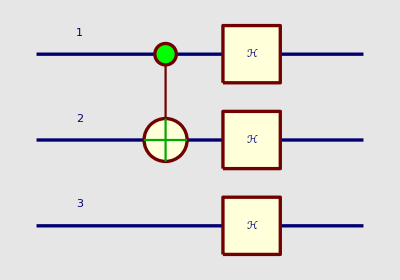

```mathematica
QuantumPlot[Subscript[ℋ, {OverHat[1],OverHat[2],OverHat[3]}]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]]
```

These two notations evaluate to the same Dirac expression, the only diference is whether gates will be plotted in the same column or not in a quantum circuit:

```mathematica
QuantumEvaluate[Subscript[ℋ, {OverHat[1],OverHat[2],OverHat[3]}]]==QuantumEvaluate[(Subscript[ℋ, OverHat[1]])^(⊗3)]
```

True

There is a notation that allows to have all the 𝒳 gates in the same column. 
Press the keys [ESC]xggg[ESC] for the template:

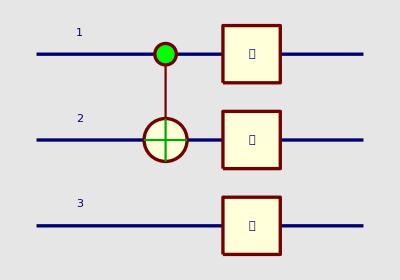

```mathematica
QuantumPlot[Subscript[𝒳, {OverHat[1],OverHat[2],OverHat[3]}]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]]
```

These two notations evaluate to the same Dirac expression, the only diference is whether gates will be plotted in the same column or not in a quantum circuit:

```mathematica
QuantumEvaluate[Subscript[𝒳, {OverHat[1],OverHat[2],OverHat[3]}]]==QuantumEvaluate[(Subscript[𝒳, OverHat[1]])^(⊗3)]
```

True

## Textbook Examples

It is a textbook exercise to show that the following circuit is equivalente to a Toffoli (controlled-controlled-not) gate. Press [ESC]her[ESC] for the "Hermitian Conjugate" (□)^† template:

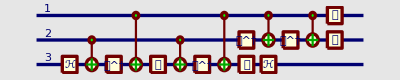

```mathematica
QuantumPlot[Subscript[𝒯, OverHat[1]]·Subscript[𝒮, OverHat[2]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·SuperDagger[(Subscript[𝒯, OverHat[2]])]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·SuperDagger[(Subscript[𝒯, OverHat[2]])]·Subscript[ℋ, OverHat[3]]·Subscript[𝒯, OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·SuperDagger[(Subscript[𝒯, OverHat[3]])]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[𝒯, OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·SuperDagger[(Subscript[𝒯, OverHat[3]])]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[ℋ, OverHat[3]]]
```

Use the option ImageSize → {250, Automatic} to have a smaller version of the circuit. 
Press the keys [ESC]->[ESC] ("Escape","Minus","Grater Than","Escape") in order to enter the arrow →

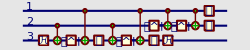

```mathematica
QuantumPlot[Subscript[𝒯, OverHat[1]]·Subscript[𝒮, OverHat[2]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·SuperDagger[(Subscript[𝒯, OverHat[2]])]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·SuperDagger[(Subscript[𝒯, OverHat[2]])]·Subscript[ℋ, OverHat[3]]·Subscript[𝒯, OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·SuperDagger[(Subscript[𝒯, OverHat[3]])]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[𝒯, OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·SuperDagger[(Subscript[𝒯, OverHat[3]])]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[ℋ, OverHat[3]],ImageSize->{250,Automatic}]
```

This is the Truth-Table of the circuit (write QuantumTableForm[ ] and copy-paste the circuit from the previous calculation inside the brackets). Notice that only the two last rows of the table are different from the table of an identity:

```mathematica
QuantumTableForm[-Graphics-]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
1 | |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
2 | |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩
3 | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
4 | |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
5 | |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
6 | |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
7 | |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩

We can see that is identical the Truth-Table of the Toffoli gate:
QuantumTableForm[ [ESC]toff[ESC] ]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
1 [TAB] 2 [TAB] 3
then press at the same time the keys ⇧-⌤ to evaluate. Notice that only the two last rows of the table are different from the table of an identity:

```mathematica
QuantumTableForm[Subscript[𝒯𝒪ℱℱ𝒪ℒℐ, OverHat[1],OverHat[2],OverHat[3]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
1 | |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
2 | |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩
3 | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
4 | |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
5 | |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
6 | |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
7 | |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩

Another textbook example. In order to enter the "controlled-controlled not" gates press the keys [ESC]ccnot[ESC]. For the "tensor product" press the keys [ESC]tprod[ESC]. For an arbitrary controlled gate press the keys [ESC]cgate[ESC]. For the arbitrary gate w, press the keys [ESC]qg[ESC]

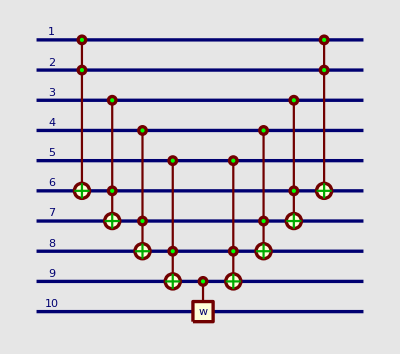

```mathematica
SetQuantumGate[w,1];
QuantumPlot[(𝒞^{OverHat[1],OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[6]]]·(⊗_(j=1)^3(𝒞^{OverHat[j+2],OverHat[j+5]})[Subscript[𝒩𝒪𝒯, OverHat[j+6]]])·(𝒞^{OverHat[9]})[Subscript[w, OverHat[10]]]·(⊗_(j=1)^3(𝒞^{OverHat[6-j],OverHat[9-j]})[Subscript[𝒩𝒪𝒯, OverHat[10-j]]])·(𝒞^{OverHat[1],OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[6]]]]
```

## Quantum Register Notation

Press [ESC]hn[ESC] [TAB]  [ESC]qr[ESC] to use the "quantum register" template in the Hadamard gate:

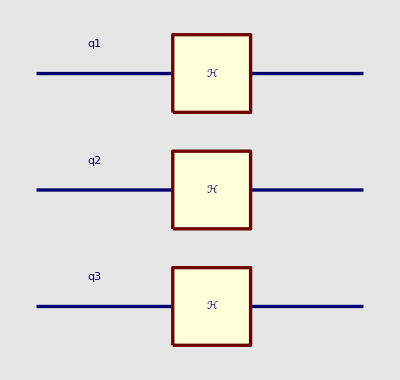

```mathematica
QuantumPlot[Subscript[ℋ, ℛℯℊ𝒾𝓈𝓉ℯ𝓇[3,"q"]]]
```

Press [ESC]hn[ESC] [TAB]  [ESC]qr[ESC] to use the "quantum register" template in the Hadamard gate:

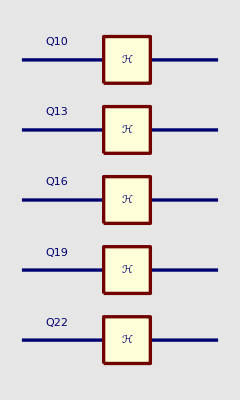

```mathematica
QuantumPlot[Subscript[ℋ, ℛℯℊ𝒾𝓈𝓉ℯ𝓇[10,22,3,"Q"]]]
```

## Powers of Quantum Gates in Circuits

The power of a gate is by default shown as a single block. Press the keys [ESC]qg[ESC] in order to obtain the gate template □_OverHat[□]

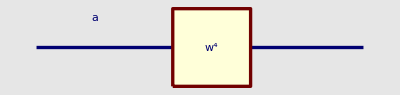

```mathematica
SetQuantumGate[w,1];
QuantumPlot[Subscript[w, â]^4]
```

Integer powers of gates are shown as several gates if the option GatePowers is set to True. Press the keys [ESC]qg[ESC] in order to obtain the gate template □_OverHat[□]

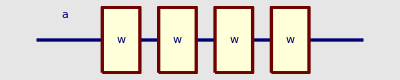

```mathematica
SetQuantumGate[w,1];
QuantumPlot[Subscript[w, â]^4,QuantumGatePowers->False]
```

## Gates of two qubits

Here is a gate of two qubits. Press the keys [ESC]qqg[ESC] in order to obtain the gate template □_(OverHat[□],OverHat[□])

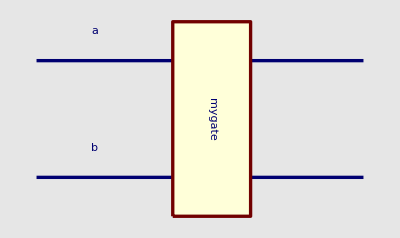

```mathematica
SetQuantumGate[mygate,2];
QuantumPlot[Subscript[mygate, â,b̂]]
```

This is a controlled gate. Press the keys [ESC]cgate[ESC] in order to obtain the controlled gate template. Press the keys [ESC]qqg[ESC] in order to obtain the gate template □_(OverHat[□],OverHat[□])

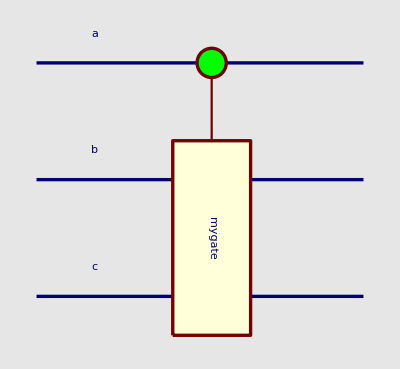

```mathematica
SetQuantumGate[mygate,2];
QuantumPlot[(𝒞^{â})[Subscript[mygate, b̂,ĉ]]]
```

This is a controlled gate.  Press the keys [ESC]ccgate[ESC] in order to obtain the controlled-controlled gate template 𝒞^{OverHat[□],OverHat[□]}[□]. Press the keys [ESC]qqg[ESC] in order to obtain the gate template □_(OverHat[□],OverHat[□])

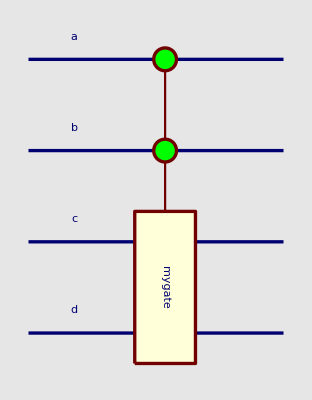

```mathematica
SetQuantumGate[mygate,2];
QuantumPlot[(𝒞^{â,b̂})[Subscript[mygate, ĉ,d̂]]]
```

This circuit shows controlled gates of two qbits, powers of gates, and initial values for some of the qubits:

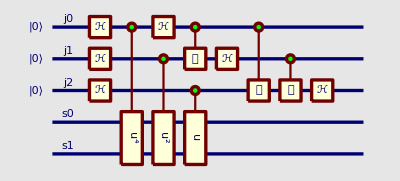

```mathematica
SetQuantumGate[u,2];
QuantumPlot[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, OverHat[j2]]·Subscript[ℋ, OverHat[j1]]·Subscript[ℋ, OverHat[j0]]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩]
```

Use the option ImageSize → {500, Automatic} to have a larger version of the circuit:

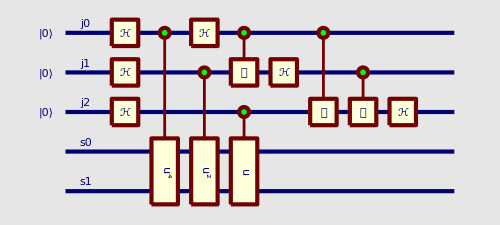

```mathematica
SetQuantumGate[u,2];
QuantumPlot[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, OverHat[j2]]·Subscript[ℋ, OverHat[j1]]·Subscript[ℋ, OverHat[j0]]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩,ImageSize->{500,Automatic}]
```

A 3D-version of the circuit

```mathematica
SetQuantumGate[u,2];
QuantumPlot3D[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, OverHat[j2]]·Subscript[ℋ, OverHat[j1]]·Subscript[ℋ, OverHat[j0]]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩]
```

-Graphics3D-

Same circuit with QuantumGateShifting→False

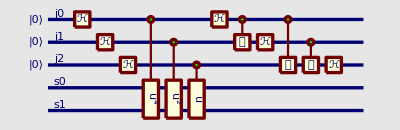

```mathematica
SetQuantumGate[u,2];
QuantumPlot[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, OverHat[j2]]·Subscript[ℋ, OverHat[j1]]·Subscript[ℋ, OverHat[j0]]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩,QuantumGateShifting->False]
```

Same circuit with QuantumGateShifting→False AND the use of the template ℋ_{OverHat[□],OverHat[□],OverHat[□]} for plotting the three Hadamard gates in the same column, see the gates next to the ket and compare with the circuit above. The ℋ_{OverHat[□],OverHat[□],OverHat[□]} template can be entered y pressing the keys [ESC]hggg[ESC]

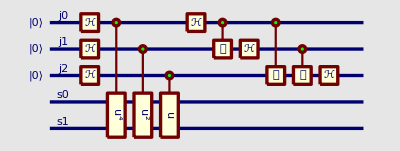

```mathematica
SetQuantumGate[u,2];
QuantumPlot[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, {OverHat[j0],OverHat[j1],OverHat[j2]}]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩,QuantumGateShifting->False]
```

Same circuit with QuantumGatePowers→False

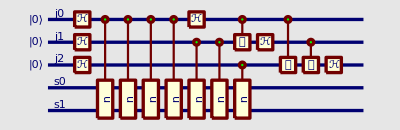

```mathematica
SetQuantumGate[u,2];
QuantumPlot[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, OverHat[j2]]·Subscript[ℋ, OverHat[j1]]·Subscript[ℋ, OverHat[j0]]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩,QuantumGatePowers->False]
```

Same circuit with qubit order specified by QubitList

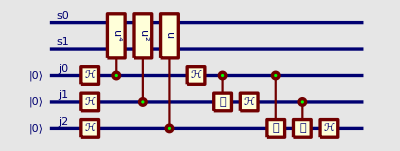

```mathematica
SetQuantumGate[u,2];
QuantumPlot[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, OverHat[j2]]·Subscript[ℋ, OverHat[j1]]·Subscript[ℋ, OverHat[j0]]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩,QubitList->{OverHat[s0],OverHat[s1],OverHat[j0],OverHat[j1],OverHat[j2]}]
```

## Measuring Meters

Next circuit shows how plot Measuring Meters in a quantum circuit. 
Notice that QubitMeasurement has not the same syntaxis as a quantum gate:

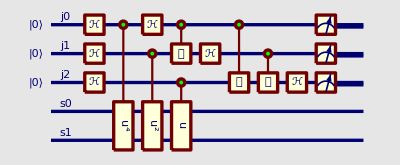

```mathematica
SetQuantumGate[u,2];
QuantumPlot[QubitMeasurement[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, OverHat[j2]]·Subscript[ℋ, OverHat[j1]]·Subscript[ℋ, OverHat[j0]]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩,{OverHat[j0],OverHat[j1],OverHat[j2]}]]
```

Same circuit with QuantumGateShifting→False AND the use of the template ℋ_{OverHat[□],OverHat[□],OverHat[□]} for plotting the three Hadamard gates in the same column, see the gates next to the ket and compare with the circuit above. The ℋ_{OverHat[□],OverHat[□],OverHat[□]} template can be entered y pressing the keys [ESC]hggg[ESC]

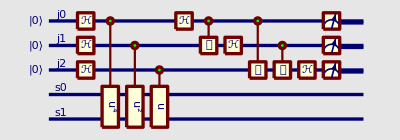

```mathematica
SetQuantumGate[u,2];
QuantumPlot[QubitMeasurement[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, {OverHat[j0],OverHat[j1],OverHat[j2]}]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩,{OverHat[j0],OverHat[j1],OverHat[j2]}],QuantumGateShifting->False]
```

Controlled gates commute with measurements in their control qubit. This means these two circuits are equivalent:

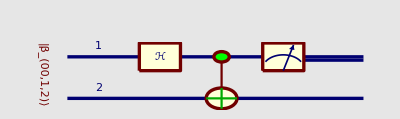
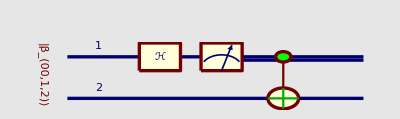

```mathematica
{QuantumPlot[ QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·|Subscript[ℬ, 00,OverHat[1],OverHat[2]]⟩,{OverHat[1]}] ],
QuantumPlot[ (𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·QubitMeasurement[Subscript[ℋ, OverHat[1]]·|Subscript[ℬ, 00,OverHat[1],OverHat[2]]⟩,{OverHat[1]}] ]}
```

It can be seen that both circuits are equivalent by writting QuantumEvaluate instead of QuantumPlot:

```mathematica
{QuantumEvaluate[ QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·|Subscript[ℬ, 00,OverHat[1],OverHat[2]]⟩,{OverHat[1]}] ],
QuantumEvaluate[ (𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·QubitMeasurement[Subscript[ℋ, OverHat[1]]·|Subscript[ℬ, 00,OverHat[1],OverHat[2]]⟩,{OverHat[1]}] ]}
```

{Probability | Measurement | State
1/2 | {{0_OverHat[1]}} | |0_OverHat[1]⟩⊗((|0_OverHat[2]⟩)/(√2)+(|1_OverHat[2]⟩)/(√2))
1/2 | {{1_OverHat[1]}} | |1_OverHat[1]⟩⊗(-(|0_OverHat[2]⟩)/(√2)+(|1_OverHat[2]⟩)/(√2))
Probability | Measurement | State,Probability | Measurement | State
1/2 | {{0_OverHat[1]}} | |0_OverHat[1]⟩⊗((|0_OverHat[2]⟩)/(√2)+(|1_OverHat[2]⟩)/(√2))
1/2 | {{1_OverHat[1]}} | |1_OverHat[1]⟩⊗(-(|0_OverHat[2]⟩)/(√2)+(|1_OverHat[2]⟩)/(√2))
Probability | Measurement | State}

## Use of Circuit Options

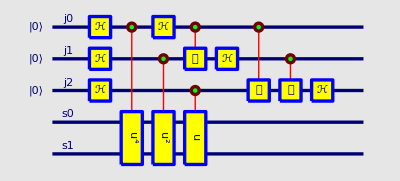

```mathematica
SetQuantumGate[u,2];
QuantumPlot[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, OverHat[j2]]·Subscript[ℋ, OverHat[j1]]·Subscript[ℋ, OverHat[j0]]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩,QuantumConnectionStyle->Directive[Red,Thin],
QuantumGateStyle->Directive[Yellow,EdgeForm[{Blue}]]]
```

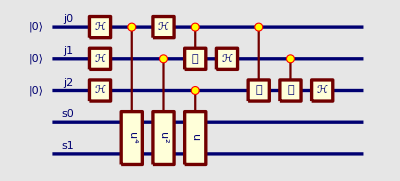

```mathematica
SetQuantumGate[u,2];
QuantumPlot[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, OverHat[j2]]·Subscript[ℋ, OverHat[j1]]·Subscript[ℋ, OverHat[j0]]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩,QuantumControlStyle->Directive[Yellow,EdgeForm[{Red}]]
]
```

```mathematica
SetQuantumGate[u,2];
QuantumPlot3D[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, OverHat[j2]]·Subscript[ℋ, OverHat[j1]]·Subscript[ℋ, OverHat[j0]]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩,QuantumConnectionStyle->Directive[Red,Thin],
QuantumGateStyle->Directive[Yellow,EdgeForm[{Blue,Thick}]]
]
```

-Graphics3D-

```mathematica
SetQuantumGate[u,2];
QuantumPlot3D[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, OverHat[j2]]·Subscript[ℋ, OverHat[j1]]·Subscript[ℋ, OverHat[j0]]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩,
QuantumBackground->Black,
QuantumGateStyle->Directive[Glow[Blue]],
QuantumConnectionStyle->Directive[Glow[Yellow]],
QuantumWireStyle->Directive[Glow[Darker[Magenta]]],
QuantumControlStyle->Directive[Glow[Green]],
QuantumTextStyle->Red
]
```

-Graphics3D-

```mathematica
SetQuantumGate[u,2];
QuantumPlot3D[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, OverHat[j2]]·Subscript[ℋ, OverHat[j1]]·Subscript[ℋ, OverHat[j0]]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩,
QuantumBackground->Black,
QuantumGateStyle->Directive[Glow[Blue]],
QuantumConnectionStyle->Directive[Glow[Yellow]],
QuantumWireStyle->Directive[Glow[Darker[Magenta]]],
QuantumControlStyle->Directive[Glow[Green]],
QuantumTextStyle->Red,
Lighting->None
]
```

-Graphics3D-

```mathematica
QuantumPlot3D[
Subscript[𝒮𝒲𝒜𝒫, OverHat[2],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]],
QuantumBackground->Black,
QuantumGateStyle->Directive[Glow[Blue]],
QuantumConnectionStyle->Directive[Glow[Magenta]],
QuantumControlStyle->Directive[Glow[Yellow]],
QuantumNotStyle->Directive[Glow[Brown]],
QuantumWireStyle->Directive[Glow[Red]],
QuantumTextStyle->Green,
Lighting->None]
```

-Graphics3D-

```mathematica
SetQuantumGate[u,2];
QuantumPlot3D[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, OverHat[j2]]·Subscript[ℋ, OverHat[j1]]·Subscript[ℋ, OverHat[j0]]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩,
QuantumConnectionStyle->Brown,QuantumGateStyle->Directive[LightYellow,EdgeForm[Green]],
QuantumWireStyle->Directive[Blue,Thick],
QuantumBackground->LightGreen,
QuantumTextStyle->Directive[Red,FontWeight->Bold,FontFamily->"Verdana"]
]
```

-Graphics3D-

```mathematica
SetQuantumGate[u,2];
QuantumPlot3D[
Subscript[ℋ, OverHat[j2]]·(𝒞^{OverHat[j1]})[Subscript[𝒮, OverHat[j2]]]·(𝒞^{OverHat[j0]})[Subscript[𝒯, OverHat[j2]]]·Subscript[ℋ, OverHat[j1]]·(𝒞^{OverHat[j0]})[Subscript[𝒮, OverHat[j1]]]·Subscript[ℋ, OverHat[j0]]·(𝒞^{OverHat[j2]})[Subscript[u, OverHat[s0],OverHat[s1]]]·(𝒞^{OverHat[j1]})[Subscript[u, OverHat[s0],OverHat[s1]]^2]·(𝒞^{OverHat[j0]})[Subscript[u, OverHat[s0],OverHat[s1]]^4]·Subscript[ℋ, OverHat[j2]]·Subscript[ℋ, OverHat[j1]]·Subscript[ℋ, OverHat[j0]]·|Subscript[0, OverHat[j0]],Subscript[0, OverHat[j1]],Subscript[0, OverHat[j2]]⟩,
QuantumTextStyle->Directive[Black,Medium,FontWeight->Bold],
QuantumWireStyle->Directive[Red,Thick],
QuantumBackground->Yellow
]
```

-Graphics3D-

```mathematica
QuantumPlot3D[
Subscript[𝒮𝒲𝒜𝒫, OverHat[2],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]],
QuantumSwapStyle->Directive[Red,Opacity[0.4]],
QuantumGateStyle->Directive[Opacity[0.4]]
]
```

-Graphics3D-

QuantumPlot has its own options, plus all the options of the standard Mathematica commands Plot and Plot3D. Following commands show a list of the options that are exclusive of QuantumPlot, together with their default value:

```mathematica
Select[Options[QuantumPlot],Characters[SymbolName[#[[1]]]][[1]]=="Q"&]
```

{QubitList→{},QubitLabels→True,QuantumGatePowers→True,QuantumGateShifting→True,QuantumBackground→RGBColor[0.9,0.9,0.9],QuantumMeterStyle→Directive[RGBColor[0,0,4/9],Thickness[0.003],Arrowheads[Small]],QuantumWireStyle→Directive[RGBColor[0,0,4/9],Thickness[0.006]],QuantumConnectionStyle→Directive[RGBColor[4/9,0,0],Thickness[0.004]],QuantumNotStyle→Directive[RGBColor[0,2/3,0],Thickness[0.004]],QuantumControlStyle→Directive[RGBColor[0,1,0],EdgeForm[{RGBColor[4/9,0,0],Thickness[0.006]}]],QuantumSwapStyle→Directive[RGBColor[2/3,0,2/3],Thickness[0.006]],QuantumGateStyle→Directive[RGBColor[1,1,0.85],EdgeForm[{Thickness[0.006],RGBColor[4/9,0,0]}]],QuantumTextStyle→Directive[Small,RGBColor[0,0,4/9],FontFamily→Verdana],QuantumVerticalTextStyle→Directive[RGBColor[4/9,0,0],FontFamily→Verdana],QuantumPlot3D→False}

## Use of Standard Graphics Options

Standard Mathematica Graphics options can be used in a Quantum Circuit using the syntax:
QuantumPlot[expression,options]

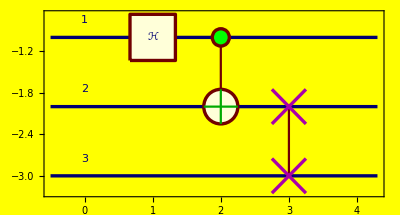

```mathematica
QuantumPlot[
Subscript[𝒮𝒲𝒜𝒫, OverHat[2],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]],Background->Yellow,Frame->True,FrameStyle->Blue]
```

Standard Mathematica Graphics3D options can be used in a Quantum Circuit using the syntax:
QuantumPlot3D[expression,options]

```mathematica
QuantumPlot3D[
Subscript[𝒮𝒲𝒜𝒫, OverHat[2],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]],
Background->Yellow,Boxed->True,Axes->True]
```

-Graphics3D-

Standard Mathematica Graphics options can be used in a Quantum Circuit using the syntax:
QuantumPlot[expression,options]

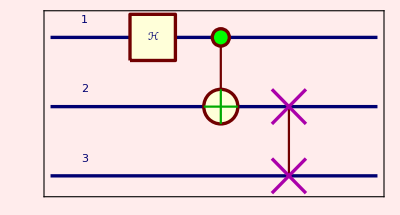

```mathematica
QuantumPlot[
Subscript[𝒮𝒲𝒜𝒫, OverHat[2],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]],
Background->LightPink,Frame->True,FrameTicks->None,FrameStyle->Thick]
```

Standard Mathematica primitives can be combined Quantum Circuit using the syntax:
Show[QuantumPlot[expression],Graphics[{primitives}],options]

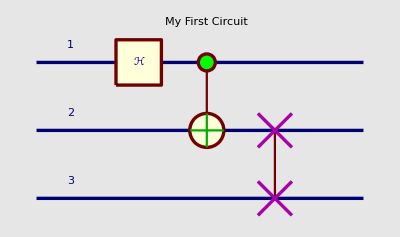

```mathematica
Show[QuantumPlot[
Subscript[𝒮𝒲𝒜𝒫, OverHat[2],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]],Graphics[{Text[Style["My First Circuit",Large],{2,-0.4}]}],Frame->False]
```

Standard Mathematica primitives can be combined Quantum Circuit using the syntax:
Show[QuantumPlot[expression],Graphics[{primitives}],options]

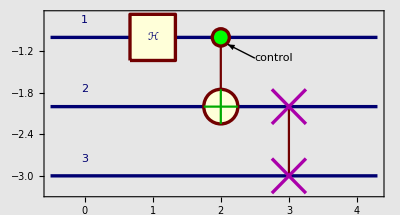

```mathematica
Show[
QuantumPlot[
Subscript[𝒮𝒲𝒜𝒫, OverHat[2],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]],
Graphics[{
Arrow[{{2.5,-1.3},{2.1,-1.1}}],
Text[Style["control",Large],{2.5,-1.3},{-1.1,0}]
}],Frame->True]
```

Standard Mathematica primitives can be combined Quantum Circuit using the syntax:
Show[QuantumPlot[expression],Graphics[{primitives}],options]

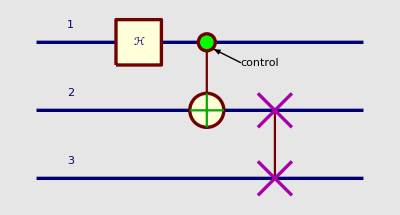

```mathematica
Show[
QuantumPlot[
Subscript[𝒮𝒲𝒜𝒫, OverHat[2],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]],
Graphics[{
Arrow[{{2.5,-1.3},{2.1,-1.1}}],
Text[Style["control",Large],{2.5,-1.3},{-1.1,0}]
}],Frame->False]
```

Standard Mathematica primitives can be combined Quantum Circuit using the syntax:
Show[QuantumPlot[expression],Graphics[{primitives}],options]

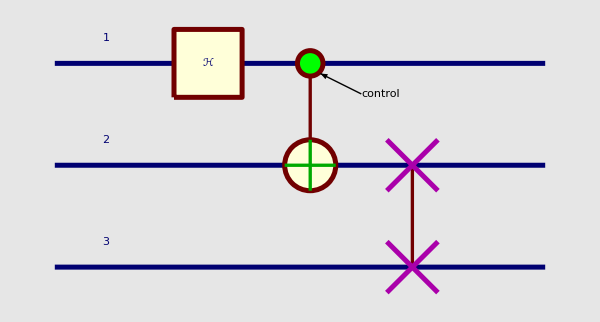

```mathematica
Show[
QuantumPlot[
Subscript[𝒮𝒲𝒜𝒫, OverHat[2],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]],
Graphics[{
Arrow[{{2.5,-1.3},{2.1,-1.1}}],
Text[Style["control",Large],{2.5,-1.3},{-1.1,0}]
}],Frame->False,ImageSize->{600,Automatic}]
```

Standard Mathematica primitives can be combined Quantum Circuit using the syntax:
Show[QuantumPlot3D[expression],Graphics3D[{primitives}],options]

```mathematica
Show[
QuantumPlot3D[
Subscript[𝒮𝒲𝒜𝒫, OverHat[2],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]],
Graphics3D[{
Arrow[{{2.6,0.3,0},{2.1,-0.9,0}}],
Text[Style["control",Large],{2.6,0.3,0},{-1.1,0}]
}]]
```

-Graphics3D-

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx